# A fast Introduction to Mathematica

Jason Harris
Wolfram Research

## Introduction

This talk gives a fast introduction to Mathematica. It is not so much intended to educate you about the use of Mathematica in Physics, rather its aim is to establish a minimum base level of Mathematica necessary for the succeeding days of the summer school. It will also focus on some points that are likely outside the scope of the other talks in the summer school.  A range of topics will be covered including the graphics system, visualization, symbolic computation, and numeric computation. However the main focus will be the core language, and demonstrating how to drive the front end and how to interact with Mathematica. Since Mathematica is such a vast system, this talk will of course be only an introduction to the core of Mathematica.

## Mathematica

Mathematica is a system for doing symbolic and numeric computations and visualization.

Mathematica is a functional language, based on rewrite rules and an infinite evaluation model. However one can also program Mathematica in a imperative fashion.

Mathematica is comprised of several million lines of code in C, C++, and Mathematica.

## History

A brief history of symbolic computation and Mathematica:

1960 - LISP (MIT, John McCarthy, etc...)

1980 - SMP (Wolfram, et al.)

1988 - Mathematica 1

1996 - Mathematica 3

2007 - Mathematica 6

2008 - Mathematica 7

2010 - Mathematica 8

2012 - Mathematica 9

2014 - Mathematica 10

## Notebook Interface

The front end uses a notebook, interface with cells, graphics, input output all mixed together.

Palettes, Preferences, etc are all notebooks

## Cells

Cell Brackets

Title cells

Input cells

```mathematica
a=1
b=2
```

Divide cells, Merge cells

## StandardForm vs TraditionalForm

### SquareBrackets vs Multiplication

Enter Random[], Factorial[5], etc. Talk about  f (b+c) vs f[b+c]

### TraditionalForm

You can convert any syntactically valid expression from StandardForm to TraditionalForm or back again using the menus.

```mathematica
∫_a^b Sin[x]ⅆx
```

```mathematica
Gamma[a]
```

```mathematica
BellB[n]//TraditionalForm
```

```mathematica
BernoulliB[n]//TraditionalForm
```

In TraditionalForm some traditional notations are recognized.

Do Γ(z)

But some TraditionalForm input is ambiguous.

You can switch to using TraditionalForm by default in the Preferences.

Switch to TraditionalForm input and output and compare f (b+c) and f(b+c)

Is f(a+b) function application or multiplication?

## Palettes and 2D Input

Open the classroom assistant, do integral

How does one enter some 2D typeset expression like the following?

```mathematica
∫_a^b ⅇ^(-x^2)ⅆx
```

```mathematica
D[Sin[x], x]
```

Tab moves between placeholders.

Note: ⅇ and e are different, as are ⅆ and d, and ⅈ and i

Entry of ∫_a^b x^2 ⅆx by Palette then by Keyboard

Subexpression selection through cntrl-.

Enter a+α, control-. ^10 and Expand

## Named Characters

Enter Pi, alpha, gamma, πd4

πd4, Mention syntax coloring

## Helpers

Command completion is your friend! ⌘-K to complete the command, and ⌘-⇧-K to template-ize the command. In v10 completion is automatic! (preferences control this)

Complete WeierstrassZeta, TraditionalForm, relation to WeierstrassP...

Insert from above! ⌘-L

## Navigating Help

https://www.wolfram.com/language/fast-introduction-for-programmers/

```mathematica
Plot
```

### Find Selected Function

### Documentation Center

### Context Sensitive Help

### Perdective Interface

# Calculator like Usage

## Integrate

```mathematica
Assuming[h/(k T)>0,∫_0^∞ ((2π ν^2) ∑_(n=0)^∞ h n ν ⅇ^(-(h n ν)/(k T)))/(c^3 ∑_(n=0)^∞ ⅇ^(-(h n ν)/(k T)))ⅆν]
```

(2 k^4 π^5 T^4)/(15 c^3 h^3)

## Solve

Solve quadratic

## Reduce

Reduce quadratic > 0

## DSolve

Reduce simple harmonic motion

## Expand

Expand (x+y)^10

## Simplify

Simplify %

% is the previous result. %n is the n^th result.

%11 /. k→α

## Output as Input

```mathematica
Expand[(x+y)^10]
```

# Core Language

## Assignment

Do basic assignment of x= 5 and then the usage of this.

```mathematica
x=Random[]
```

0.00876814

```mathematica
y:=Random[]
```

```mathematica
Table[y,{10}]
```

{0.925756,0.112791,0.912471,0.253004,0.840514,0.810677,0.749616,0.596422,0.264889,0.75286}

```mathematica
Table[x,{10}]
```

{0.00876814,0.00876814,0.00876814,0.00876814,0.00876814,0.00876814,0.00876814,0.00876814,0.00876814,0.00876814}

### Set (=)

### SetDelayed (:=)

Use Random illustrate the difference. y :=Random[],  Table[y,{10}]

## Function Application

Using f@ ... is equivalent to f[ ...]

```mathematica
f[g[h[blah]]]
```

f[g[h[blah]]]

```mathematica
f@g@h@blahh
```

f[g[h[blahh]]]

(Note in some other functional languages one can just use f g h arg.)

You can also apply a function in a trailing manner using expr // func

```mathematica
y=.
```

```mathematica
(x+y)^10//Expand//Factor
```

(x+y)^10

```mathematica
Factor[Expand[(x+y)^10]]
```

Do (x+y)^10//Expand then Simplify this

## Expressions

### General Expressions

A list is something of the form

```mathematica
{a,b,c,...}
```

```mathematica
{a,b,c,d}//FullForm
```

List[a,b,c,d]

Everything inside Mathematica is an expression of the form (apart from terminals):

```mathematica
head[Subscript[argument, 1],Subscript[argument, 2],...]
```

```mathematica
a+d^2+f+b*c//FullForm
```

Plus[a,Times[b,c],Power[d,2],f]

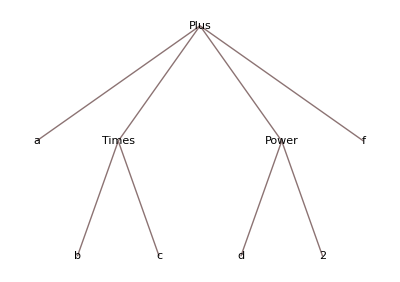

```mathematica
a+d^2+f+b*c//TreeForm
```

```mathematica
%7
```

(2 k^4 π^5 T^4)/(15 c^3 h^3)

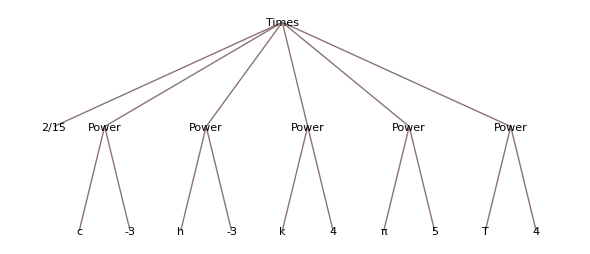

```mathematica
%7//TreeForm
```

### FullForm

Talk about precedence and grouping and the FullForm of x^3+(1+x y)^2

Do TreeForm @ %

Do TreeForm of our black body output

### Part

expr⟦i⟧ yields the i^th part. expr⟦0⟧ yields the head.

Do parts of f[a, b, c, d]

```mathematica
f[a,b,c,d]
```

```mathematica
Part[f[a,b,c,d],-1]
```

```mathematica
f[a,b,c,d]⟦-2;;⟧
```

f[c,d]

More generally Part can take a list, or “Spans”

Do f[a, b, c, d]⟦{1,3}⟧

Many functions have generalizations.

Get FullForm of %

### Extract

We can use extract to Extract multiple parts out of an expression. For example to extract y and c out of f[a, b[x, y], c, d]

Extract[f[a, b[x, y], c, d], {{2, 1}, {3}}]

```mathematica
f[a, b[x, y], c, d]
```

```mathematica
f[a, b[x, y+γ], c, d]⟦2⟧⟦2⟧⟦1⟧
```

y

```mathematica
Extract[f[a, b[x, y+γ], c, d],{{2,2,1},{3}}]
```

{y,c}

## Structure Manipulation

### Map

You can use Map to map a function onto a list or more generally onto an expression.

```mathematica
Map[foo,h[a,b,c,d]]
```

h[foo[a],foo[b],foo[c],foo[d]]

```mathematica
foo/@{a,b,c,d}
```

{foo[a],foo[b],foo[c],foo[d]}

Do a map of foo over g[a,b,c,d]

Map has the short form /@

Transform last output

### Apply

Apply will replace the head of an expression.

```mathematica
Apply[bar,f[g]]
```

bar[g]

```mathematica
bar@@f[g]
```

bar[g]

Apply has the short form @@

Transform last output

Apply opperates at different levels.

```mathematica
ans=foo/@{a[t],b[g],c[y],d[y]}
```

{foo[a[t]],foo[b[g]],foo[c[y]],foo[d[y]]}

```mathematica
Apply[bar,ans,{2}]
```

{foo[bar[t]],foo[bar[g]],foo[bar[y]],foo[bar[y]]}

```mathematica
bar@@@ans
```

{bar[a],bar[b],bar[c],bar[d]}

Apply at level 1 has the short form @@@

### Table

```mathematica
Plus@@Table[i,{i,1,10}]
```

55

```mathematica
{1,2}+{3,4}
```

{4,6}

```mathematica
Plus@@Plus@@Table[i^2/(√j),{i,1,5},{j,1,5}]
```

165/2+35/(√2)+10 √2+46/(√3)+3 √3+11 √5

Do 1D table, apply Plus, use Sum, contrast to symbolic sumation

Then 2D table with MatrixForm

Plus @@ Table[i^2/(√j),{i,1,5},{j,1,5}]

### Take

Take allows us to take a subexpression of an expression

```mathematica
f[a,b,c,d,e]
```

```mathematica
Take[f[a,b,c,d,e],-2]
```

f[d,e]

Take the some elements from an expression, from the beginning, and from the end apply list, compare to part of Span

### Drop

```mathematica
f[a,b,c,d,e]
```

```mathematica
Drop[f[a,b,c,d,e],-1]
```

f[a,b,c,d]

Drop some elements from an expression, from the beginning, and from the end

## Functions and Pattern Matching

Define some simple rules without patterns

```mathematica
MySquare[x_]:=x^2
```

```mathematica
MySquare[(t+γ)/Sin[x]]
```

(t+γ)^2 Csc[x]^2

```mathematica
fac[n_]:=n fac[n-1]
fac[0]:=1
```

```mathematica
fac[5]
```

120

```mathematica
fac[1.5]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fac[-1020.5 - 1].

Hold[1.5 fac[1.5-1]]

### Single Pattern variables

A variable with a trailing underscore ie x_  is a "pattern" variable. It is included on the lhs of a definition but not the right hand side.

Do function MySquare for x^2

Do factorial

### Restricting the Match of a Pattern

```mathematica
ClearAll[fac]
fac[n_Integer/;n>0]:=n fac[n-1]
fac[0]:=1
```

A pattern of the form var_h will only match expressions whose head is h.

Evaluate our factorial for ' a', and then restrict to just _Integer

A pattern of the form pat /; expression will only match when expression evaluates to True.

Restrict our factorial to only fire when the argument is >= 0.

ClearAll[factorial]
factorial[0] = 1
factorial[n_Integer] /; n >= 0 := n factorial[n - 1]

A pattern of the form pat ? func will only match when func applied to the match evaluates to True.

```mathematica
EvenQ[π]
```

False

```mathematica
fud[a_?EvenQ]:=a^2
fud[a_?OddQ]:=-a
```

```mathematica
fud[π]
```

fud[π]

Do even is squared, odd is negated

### Boolean functions

Many of the functions in Mathematica which return a boolean value end in the letter 'Q'. Eg EvenQ, OddQ, AtomQ, NumberQ, SameQ, MatchQ, FreeQ.

```mathematica
MatchQ[foo[x^3,y,z,t],_[x^_,_,_,t]]
```

True

### Pattern matching and FullForm

You frequently need to use FullForm to diagnose problems

```mathematica
fud[a_/b_]:=bob[a,b]
```

```mathematica
fud[Rational[a_,b_]]:=bob[a,b]
```

```mathematica
Rational[a,b]
```

Rational[a,b]

```mathematica
q/w
```

```mathematica
fud[w/(q+ω)]
```

bob[w,q+ω]

```mathematica
fud[1/2]
```

bob[1,2]

```mathematica
MatchQ[1/2,a_/b_]
```

False

```mathematica
q/w//FullForm
```

```mathematica
Times[_,Power[_,-1]]
```

```mathematica
1/2//FullForm
```

Rational[1,2]

Do MatchQ[1/4,a_/b_]

Pattern matching is a structural matching and not a semantic matching.

## Rules

A rule is of the form lhs → rhs and using rules we can perform replacements. Replace has the short form /.

```mathematica
foo[bar[x],x^2,g[x]]/.x->α
```

foo[bar[α],α^2,g[α]]

Add Power->h

Mention Solve result returns rules

:> (RuleDelayed) will do its evaluation when the rule is applied like := (SetDelayed)

```mathematica
{x,x,x}/.x:>RandomReal[]
```

{0.798711,0.954804,0.0883122}

```mathematica
{x,x,x}/.x->RandomReal[]
```

{0.829516,0.829516,0.829516}

Change above to use →

Rules can contain patterns and are of the form pattern → expression. Just like in functions we include the pattern variables on the lhs and then the naked expressions on the rhs.

```mathematica
ClearAll[fac]
facRule = {fac[0]->1,fac[n_]->n fac[n-1]}
```

{fac[0]→1,fac[n_]→n fac[-1+n]}

```mathematica
fac[5000]//.facRule
```

422857792660554352220106420023358440539078667462664674884978240218135805270810820069089904787170638753708474665730068544587848606668381273633721089377278763127939036305846216064390447898698223987192970889621161265296832177550039924219683703146907264472878789790404754884162215226671928410969236910449565971736352948400223840381120644820230857671104502306174894755428309761781724040805324809927809328784055486199364548291211876258248802189173977900050213212598043639244626460770511358846595108675470585833924655225589035474435988347383178988034633008458631510209091509935653820010933047965742556741930917055172805200236075085991197635228755907902043369743123506916831211924495971556267407521462198986233088625998302859864857578749445963115286970886710046268423648178989905454690861391613218344174148807186234448114831209490361196546872767755617886828720269104814092456410341835975604276458161513178575901661071782544156980883359372729995603371371200471049437656291142488605335299499642300699972204918120100819059439140675053265004775533850899097945101551091486907004407119572336026243368132330218709287699196806656569752790422258267841561083376425781032629202687211070274681394351128601502326190649959171897364176378436491219709109840944514895358959103804176941956657834822071749105512752639148381172052604826965162642710094919393332661030104360530459117014557209584714353721948246686793467375904872268133410207860903657108806376616249749507413107077401682180585945526445171409277469230062697511346044174567946735828782261629584248675157379172942724178783105429858245117575511884506574424827574660800238588378492396247368761507015767725898321128632295537044902516387925127590841791744640466913531047347984464996154595542013996317357476301740036796192919942190762895445656261767041799538161133387312823511534152581309087915883638351664797225912944270653557142511737323807232632958121797916679692329687096923901003255574789055099807487061047230646195984955239657612208673866514171699307557691897902675157342075864796345338446835085965490727326321910504064289713096224505162064669468098869917122127404504020684923266241760132910227866687270305284709452526825496617772499645206699836925910690894082637401043498371591126455822280606361394115344316771769934353664284928294436414769615881993661388255577487709937004594753907845149034434521174560594039916268444697661821387470705325559577933196460996662145377564935474169708562389214773222865507182490430016186142192760452307670621142961767274704123616107220009743758647492753665149532164780849075146330071016691313420662882562618283865836983632108760710427516073348347788414796732427080410860761841281888307115098982135338406610652147087046874760995427473673509451553599769040367353385551052571682650317682405743993414862392331981432579182193321898940450865013610998098383993110996355981328001049731588596312131853801205046787642910669365600437305633431984879048998524701293300789344532868156679762880495532846386020133480265279836946393384995675049993707814746561543438930431384237878981847802886009971088695632988347711863122382785963653115132377931373647397429369411499028751972227999545182615488298951151926682112451355318472209990435355949887299922035062039816011086376236539782172380237846650673624510635034423187315338308212043804710999419227821039747552717416043890169723961305549371844836119803565896062025009093664399360172007383613354405094329072476518909502507724675841989412224659392163116352038147362479528539732089309533421910635702805576629720156556510767780805933453631121829561792887673002802450932122778852968418208261778476955644980385691275787372678040959158711733971103165232678060798127609246173504120182666874262805385275843979167609007743380748420751185119102921960339376280986753665085212869255321536787932521882574101866137054328973735862725370178558806639851350386944039604928258820180419178073649693885802597758398892014389747165465973510852605706234402069637065660129535734043582961473427275805630839510667375349259659518575646939723218275780003250593895303820539697558870511543073920827422440516299708739599768461206246629098112368012579891284802505094028916959765079395437191311379314427405135599630375642214527294341797246187597964074239147838993541565834716156858499036773056611353833367087548900413091981676330749041510337597307246885839246941715548295730750618505881581959528992660225626903439573313450666972952115230668696227920947779974336574472673471408928071411283888082693377378077293104110767513639476200610858040596019639058015761002337463869352228385801434957178125581445862930042479404065736859862007914604590255413929950088044710384758990326548097338166940500085452723713571394902463820308668541802838317527668064278489561005755859991718966786449154063570014497194249878920859731254275567514575206399118150736397483102490793841725653421894276769116598153430084637087769510295415136551734675054015239706042571746001089968440498845985477977905031632568489156557231006499726498721480800181770357701502983008879487243887718884416833034708723239505377642232944095773219137582371673924704216723002256883135779230394688900662466182532658490724406767024939579697217467485562998183149665611743997680482094166257463879660305171274925119226367615337524381656217330771650129520988754856467131862602387619964334867961514408328902061082833180891221325853682856469916007952105166960451695430614212305743006877217407155473217957577017595967640563812729153867513698712395570542350999228605975469962186195531354132139126436676900465429996811680550737866770665988027062972502001882845886145344368771455361304414465613369092862748276981946836480550952968681758714859972973082332924094777085275279923304892719633314751563311192746150389219290616780607901383451137066300684376267199885515143681266137319912103235469786756421210624899005553564022924345831264231038363416781719908354140411717740185950606674198348143345444247191436828225654380047860390575922417071802670646875454211626958746795398540784464654140381751149965273621123540880166990280149033225139460832668170930713868826549977374286127789417784752681328371818759103642140881783220739808059714203285309721443041845459183002833408705783138284973283761286182927136745161897366207237396132790944984014154408304074405393067540767126182547597130843470311389815695365971788564022750674237400323621850094765267521941901241387478279883426470873616812485384444012772521050072279315853096279121131160167772077952572613800240684421885453537121341902236379684012385255288607189967725694227433323948595075570839061877450159652184414998155476107548008054192318436948191732631430603548399790783307267636729090980772827355854348032260067472537097785464567761181807367424367391769863758072145859791485033700592994963793369100283444558089838054017635403737133019311293080958287612107380374800660269767842888358265737486556785868822015143046249655995760379768685318192365806469199584071845493606922169776137542662239658644989770921478134709127917460871630220821981434654245065731262683089579031012893360788644107230184805400373136014216229159146992019884148290014414312800903102107833305090238435726779416177246873411503598700003151092815700331081727415624680432977205070450456683898626301702989301145364477416856732512330376477881749036052572605520684370616116539755132541369303867783267208227323664249206432363089268768826650939691861683271739757479552993242406186992420363781929485368098035256331092448215269276219116259145886393677034653480367887126133367116968226450914997055448521259751870084720025674658752403932061045903070039438252019383102480929019684602472171298321628237994627125366359971898374425099120673688383738299653892030662843074547559074235345274029211606091346327684749522046010409575607348155101677203187580089224494752922031093841661588823584993931745149914395557357641584185479831702428523965451087525425464777294595230360946416541997797947136806344915998772409176443137371178542210740572121166868692153240490080384205921192622875440898261478908123698956367080804687628524499897440855677969456909042340530355943524640751677873953113928698614347227572144946891896093294375476741234907792754338349412323060078767610089949156126934038921148370217193387617823370358925817112869563450001367619897145400986643461922197676975930010555225198913002123021780831934330880446592954552165911855939202579781122952065357362914478404946474565003115498072056580360667380889572746464375428055819322299305089287806874537401327100274428317925355003451536693172112088227603942809788645727306979971285649576934354004030728440581746648376658498039958964243370183454151720285337810904113124462432903353964296651109482836884580127588701293156099225044518125460113274986014470437757313881001319276124676116614833528935557503106018449788994378274613854651708241613167681463911870000812845144341406739985430072772303758111613511094355614896323929750846383152930263582535361784837558519666949972251935515953807207838615142130284450051795239760968433198292598921623223582396390262548856855875458198371559008447860086745945709118128793228222051767509371866110013193625845223493949829511199280837860523506412769337548130609594264463425077601147334209139128541628183172262143783062962408149391997187528106367348876678481602342743230027158192404187686545826519361990687336892886715133840245486110982482004482721799496658712257174429044916781194824165631560303473833317665121218052780795958220298330611945164019413315550379662980215357680731124530585915969709973988055743550083279071844959752353594644354789680372126344509423070253995102864458237454677761013556916212309752286152053213998745673034127676503369636682306665552051562491132528926155863868503100849180920507680658265915276163719928694258350604859732273949286080260640627521341007801815105623787926212039424781833439433877206395801115809084190794320195178235740190546595990289617711776195270354051193727229722248442080440098750369411277686593022133010625031862085145076421052980508837197986052557750303949606158442838846866137510968441567309838079394349570013029265177957120625555851951313574029897589283475525334409858911400694449308432874005015554332587793895080241128538758725945136400838324944471346436826148195406004114845870234072926697740631325878634790667698266181501256117692275715291249164821702372884416357600996851100939411444677628186007072278522314941048564396255796808221289935799262208553889221164765220850367706476491496133789353761537391569177822237744837614120253342622508007300513473422771427333106345971803240244226950458090539326689103619381998838844036231795282435495362489670734155948067688515321073064476077859628627852283657244564306449096277517172656954238392941958409527253281659572534531428389629894005886539486824117113929627356938973482935854650278689437014798383826002058208853517073216288725214522205265969614962147884840129004507737252424605074339660818182960296019196314124998538422017695110361380561701016357743542531148669369994130940908368220071936435111978592782493491477052187226546109199597269439152400467901173602521030051886080337084840114810246351288263986170081804888380750203521448348740849154718714478857809574515499505005070789428842888410027877777455981132319940624176532148686316581736774410084063436959989519288310869124517866342559353458242589411390516469440377562665821577845936829909679754548350510473633770839151033854639602753486401635204633884342346714935641429160856846724874244782055113759168236472297793612971080302530934478115527737540458968990354808058309381267323593563098546564376209385371052808344607189076003388781618019853273759498566916704703448438363503416368325266403224174519476678140428319327482851882140344319384445475456765253419659194332132585432270070759038565239668227171300009189122050845185261514627937717597528852978637931711212529529443323757910072909001703558763798612480281463093944391916950129336315045285163539312868586427437296109446101235604877439863299611899755965996608749049271167685268675335991297583209089553296409523640116060078495005377892783750147344122123777907727134146647404489837589487675423294546899354220341669961366698976529978580795899055864050388507083137333076839766882463680992355219727241831735127646189112380485883115569477888101759708977682149644340317924443085170303692214137621194388641989508360339306459037361842937028710758321966607546113761076362543928614316242890754021082233620012309384737312220374269033838579928678572939434168287053763374091938184632261131740934278117918891642447513543478446040549455379834556163353815868441692054518698919434175386663900335756765603264363767906721626620330878425545157208117246381251512669846685887209013144861632560461019513371814585249988176629925142145014710206193190373671380347663431029705222414785030188275106347446241258707937339085095757724316735066885094208761536164440443755860160625837091300574162065273670941888667964570550744724714137001968165215954380698515999483361357521322106131884771926641942395351412233546746461491743013475866037338176532604557402925472279360288926189385899695656876783017186873988763887625972743976062813263446647679413679726184933395074665820441677989806604203937116666336696282569349097348391155869004856032512219241534268522369316036765491047702733521540143168338872968405443296967684036073182435336224865433823598123544167514608340781166661858781733980624199254577853462678039039937557802759942957205281043775666979396838109341118959475766220191217535093638985465283078692370662512323684390235587636228324657161183714078807661162179517887972801841572019639084400269037450381192797170314489871815031319992111563908303017288012610642062005359240278277393918026391717720136125984776933980647063763022608885359937595079088789081791802195768033381968605120487107610874898411568740159953020639098138993261095538868264084012160831040525974539251576403732889086736948366404734622708560040891610782221943405179794550155347682966855320097501905581419914591124181501062255627411231571377358697194374130822027383843815940638571387913337592362330440453487233047240668784133333047898995255221468847973813568083995644533005222551320155267768895412770329278670827490041172076663112783638152343547681663121189086864991380236281775275946061211813342054791801619220346912760381900528012343973598270461499814511324618195658528232044658270082064934680251556511272822083811563192256509945201222666603226059396247019707668580396286975551115189973049085051758765306785758000660424066894170620303846785860257370634352599586885088679654004465187790208942935153217316750113738031466034642429489076322228133763299919641336502028627289268087560036613770607463575515079087982099722660130472907825746908175451952405573791313113170617323191598673971588373108168916968657704150695512947652386134815766967580364762005289060222744531744305498402863048850869557761528650326080941160688570698894762046478500884303973107412774191961697450517110329082815201273888663422631492147090220016940636504812047036016738602290671629816411198202268607961324739550057567564568204754619040423011062371367395995678940884705976859514505017241517746017351430990972615509378334720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

We can use replace repeated to repeatedly apply a set of rules until the result can no longer change.

## Pure Functions

A pure function (or lambda function in other terminology) can be thought of as a small unnamed utility function.

```mathematica
MySquare[x_]:=x^2
```

```mathematica
(#^3&) /@ {2,f,Sin[x]}
```

{8,f^3,Sin[x]^3}

```mathematica
(b↦b^2)[4]
```

16

```mathematica
(#^2-#2&)[a,b]
```

a^2-b

Use (a↦a^2)

Use (#^2)

RootReduce

### Pure functions of more than one variable

### Task: sort a list on the second argument of the items.

```mathematica
l={f[1,4],f[4,2],h[6,1],g[2,3]}
```

{f[1,4],f[4,2],h[6,1],g[2,3]}

```mathematica
(#1⟦2⟧&)/@l
```

{4,2,1,3}

```mathematica
SortBy[l,(#1⟦2⟧&)]
```

{h[6,1],f[4,2],g[2,3],f[1,4]}

```mathematica
Sort[l,(#1⟦2⟧>#2⟦2⟧&)]
```

{f[1,4],g[2,3],f[4,2],h[6,1]}

Define SortFunc[_[_, a_], _[_, b_]] := a < b

Sort[{f[1, 4], f[4, 1], g[2, 3], h[6, 1]}, #1[[2]] <= #2[[2]] &]

SortBy[{f[1, 4], f[4, 1], g[2, 3], h[6, 1]}, #[[2]] &]

## Other Structuring commands

### Inner

Task: multiply the elements of two lists together. Then generalize to doing a general operation not just multiplication.

```mathematica
Inner[Times,{a,b,c,d},{w,x,y,z},g]
```

g[a w,b x,c y,d z]

Inner[Times, {a, b, c, d}, {w, x, y, z}]

Note there is Outer as well which will act as an "outer" product.

### Cases

Cases[expr, pattern] picks out all of the parts of expr which match pattern.

Task: pick the even powered terms out of a list.

```mathematica
{x^2,x^3,x^6,y^9,x^7}
```

```mathematica
Cases[{x^2,x^3,x^6,y^9,x^7},_^(_?OddQ)]
```

{x^3,y^9,x^7}

Cases[{x^2,x^3,y^6,z^7},x_^(_?EvenQ)]

### Select

Task: pick the even powered terms out of a list.

```mathematica
Last/@{x^2,x^3,x^6,y^9,x^7,h[3,4]}
```

{2,3,6,9,7,4}

```mathematica
Select[{x^2,x^3,x^6,y^9,x^7,h[3,4]},OddQ@Last@#&]
```

{x^3,y^9,x^7}

Select[{x^2,x^3,y^6,z^7},EvenQ[Last[#]]&]

### Length

```mathematica
Length@h[a,b,c,d]
```

4

Length @ {a,b,c,d}

Switch head

## Multi Argument Patterns

A pattern of the form x__ will match one or more arguments.

A pattern of the form x___ will match zero or more arguments.

```mathematica
f[a_,___,a_]:=g[a,b]
```

```mathematica
f[w,r,t]
```

f[w,r,t]

```mathematica
bub[l___,a_,b_,r___]:=bub[l,b,a,r]/;b<a
bub[args__]:={args}
```

```mathematica
bub[3,4,7,8,9,2,2,4,9]
```

{2,2,3,4,4,7,8,9,9}

Task : sort the elements of a list

```mathematica
ClearAll @ MySort
```

Do bubble sort

### The FullForms of Patterns

Since everything is an expression, What is the corresponding fullform's of some of these patterns.

```mathematica
FullForm[x_]
```

Pattern[x,Blank[]]

```mathematica
FullForm[x_Integer]
```

Pattern[x,Blank[Integer]]

```mathematica
FullForm[x_Integer/;x>0]
```

Condition[Pattern[x,Blank[Integer]],Greater[x,0]]

```mathematica
FullForm[x_Integer?EvenQ]
```

PatternTest[Pattern[x,Blank[Integer]],EvenQ]

## Summary: Core Language

Everything is an expression

Rules applied in order of more specific to more general

Mathematica uses an infinite evaluation model

Match anything var_

Match anything with head h var_h

Match one or more things var__

Match zero or more things var___

ReplaceAll (/.)

Map (/@)

Apply (@@)

Condition (/;)

PatternTest (?)

= vs :=

→ vs :>

Pure functions (#^2 &)

## StyleSheets

Instead of changing individual words with different styles, add styles to the style sheet. Then if you ever need to, you can change a style in the style sheet and all uses of the style will change uniformly in the notebook.

Add styles here.

## Option Inspector

You can use the option inspector to change settings at a deep level.